## Merger rate

Original PDF function

```mathematica
mMin=1;
mMax=130;
```

```mathematica
Pm[m_,p1_,p2_,p3_]:=Piecewise[{
{p1,1<=m<=10},
{p2,10<m<=40},
{p3,40<m<=80},
{(1-9p1-30p2-40p3)/50,80<m<=130}
}
]
```

```mathematica
Integrate[Pm[m,p1,p2,p3],{m,mMin,mMax}]
```

1

Binary PDF function

```mathematica
Integrate[Pm[m,p1,p2,p3]/m,{m,mMin,mMax}]^-1
```

50/(Log[13/8]-9 p1 Log[13/8]-30 p2 Log[13/8]-40 p3 Log[13/8]+50 p3 Log[2]+50 p2 Log[4]+50 p1 Log[10])

```mathematica
mpbh[p1_,p2_,p3_]:=50/(Log[13/8]-9 p1 Log[13/8]-30 p2 Log[13/8]-40 p3 Log[13/8]+50 p3 Log[2]+50 p2 Log[4]+50 p1 Log[10])
Pm[i,p1,p2,p3]*mpbh[p1,p2,p3]/i
Fm[i_,p1_,p2_,p3_]:=(50 (Piecewise[{{p1, 1≤i≤10}, {p2, 10<i≤40}, {p3, 40<i≤80}, {1/50 (1-9 p1-30 p2-40 p3), 80<i≤130}, {0, True}}]))/(i (Log[13/8]-9 p1 Log[13/8]-30 p2 Log[13/8]-40 p3 Log[13/8]+50 p3 Log[2]+50 p2 Log[4]+50 p1 Log[10]));
Integrate[Fm[m,p1,p2,p3],{m,mMin,mMax}]
```

(50 (Piecewise[{{p1, 1≤i≤10}, {p2, 10<i≤40}, {p3, 40<i≤80}, {1/50 (1-9 p1-30 p2-40 p3), 80<i≤130}, {0, True}}]))/(i (Log[13/8]-9 p1 Log[13/8]-30 p2 Log[13/8]-40 p3 Log[13/8]+50 p3 Log[2]+50 p2 Log[4]+50 p1 Log[10]))

1

```mathematica
{m10,m20}={30,30};
logM0=0.8714109083376727;
M0=7.437224791850505;
logf0=-2.5487351805854974;
f0=0.002826603025098389;
α0=2.4081116862468503;
```

```mathematica
Integrate[l^(-21/37)*Fm[l,p1,p2,p3],{l,mMin,mMax}]
```

(37 (-13 2^(27/37) 5^(16/37)+4 130^(16/37)-26000 p1+117 2^(27/37) 5^(16/37) p1+2600 10^(16/37) p1-36 130^(16/37) p1+1300 2^(11/37) 5^(16/37) p2+390 2^(27/37) 5^(16/37) p2-2600 10^(16/37) p2-120 130^(16/37) p2-1300 2^(11/37) 5^(16/37) p3+1170 2^(27/37) 5^(16/37) p3-160 130^(16/37) p3))/(10920 (-Log[13/8]+9 p1 Log[13/8]+30 p2 Log[13/8]+40 p3 Log[13/8]-50 p3 Log[2]-50 p2 Log[4]-50 p1 Log[10]))

```mathematica
1.32*10^6 fpbh^(53/37)/mpbh[p1,p2,p3]^(53/37)(i*j)^(3/37)(i+j)^(36/37) Fm[i,p1,p2,p3]*Fm[j,p1,p2,p3]*  (37 (-13 2^(27/37) 5^(16/37)+4 130^(16/37)-26000 p1+117 2^(27/37) 5^(16/37) p1+2600 10^(16/37) p1-36 130^(16/37) p1+1300 2^(11/37) 5^(16/37) p2+390 2^(27/37) 5^(16/37) p2-2600 10^(16/37) p2-120 130^(16/37) p2-1300 2^(11/37) 5^(16/37) p3+1170 2^(27/37) 5^(16/37) p3-160 130^(16/37) p3))/(10920 (-Log[13/8]+9 p1 Log[13/8]+30 p2 Log[13/8]+40 p3 Log[13/8]-50 p3 Log[2]-50 p2 Log[4]-50 p1 Log[10]))//FullSimplify//N
```

(fpbh^(53/37) (i+j)^(36/37) (1/(0.485508+110.76 p1+54.7495 p2+15.237 p3))^(21/37) (3873.23+7.01778×10^6 p1+1.30948×10^6 p2+232650. p3) (Piecewise[{{p1, 1.≤i≤10.}, {p2, 10.<i≤40.}, {p3, 40.<i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}]))/((i j)^(34/37) (0.00438343+1. p1+0.494309 p2+0.137569 p3))

```mathematica
Clear[i,mergerRateDensity1st]
mergerRateDensity1st[fpbh_,i_,j_,p1_,p2_,p3_]:=(fpbh^(53/37) (i+j)^(36/37) (3873.227220915098+7.017783302046575*^6 p1+1.309479386727924*^6 p2+232649.95335141555 p3) (1/(Log[13/8]-9 p1 Log[13/8]-30 p2 Log[13/8]-40 p3 Log[13/8]+50 p3 Log[2]+50 p2 Log[4]+50 p1 Log[10]))^(21/37) (Piecewise[{{p1, 1≤i≤10}, {p2, 10<i≤40}, {p3, 40<i≤80}, {1/50 (1-9 p1-30 p2-40 p3), 80<i≤130}, {0, True}}]) (Piecewise[{{p1, 1≤j≤10}, {p2, 10<j≤40}, {p3, 40<j≤80}, {1/50 (1-9 p1-30 p2-40 p3), 80<j≤130}, {0, True}}]))/((i j)^(34/37) (0.004383434449244752+1. p1+0.49430877240911064 p2+0.13756852497343655 p3))
```

```mathematica
mergerRateDensity1st[fpbh,i,j,p1,p2,p3]/.{p1->0.1, p2->0.2,p3->0.3,i->10,j->30,fpbh->0.001}
```

0.126092

```mathematica
(*Clear[normalFactorMergerRateDensity1st,normalizedMergerRateDensity1st];
normalFactorMergerRateDensity1st[f_?NumericQ,α_?NumericQ,M_:5]:=NIntegrate[mergerRateDensity1st[f,m1,m2,α,M],{m1,M,mMax},{m2,M,mMax},PrecisionGoal->3];

normalizedMergerRateDensity1st[f_,i_,j_,α_,M_:5]:=mergerRateDensity1st[f,i,j,α,M]/normalFactorMergerRateDensity1st[f,α,M];
normalFactorMergerRateDensity1st[f0,α0]
normalizedMergerRateDensity1st[f0,m10,m20,α0]
NIntegrate[normalizedMergerRateDensity1st[f0,m1,m2,α0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3]*)
```

```mathematica
Integrate[l^(-42/37)*Fm[l,p1,p2,p3],{l,mMin,mMax}]
```

-((37 (169 2^(17/37) 5^(32/37)-8 130^(32/37)+6760000 p1-1521 2^(17/37) 5^(32/37) p1-67600 10^(32/37) p1+72 130^(32/37) p1-5070 2^(17/37) 5^(32/37) p2-16900 2^(22/37) 5^(32/37) p2+67600 10^(32/37) p2+240 130^(32/37) p2-15210 2^(17/37) 5^(32/37) p3+16900 2^(22/37) 5^(32/37) p3+320 130^(32/37) p3))/(5678400 (-Log[13/8]+9 p1 Log[13/8]+30 p2 Log[13/8]+40 p3 Log[13/8]-50 p3 Log[2]-50 p2 Log[4]-50 p1 Log[10])))

```mathematica
1.59*10^4*fpbh^(69/37)/mpbh[p1,p2,p3]^(69/37)k^(6/37)(i+j)^(6/37)(i+j+k)^(72/37)Fm[i,p1,p2,p3]*Fm[j,p1,p2,p3]*Fm[k,p1,p2,p3](-((37 (169 2^(17/37) 5^(32/37)-8 130^(32/37)+6760000 p1-1521 2^(17/37) 5^(32/37) p1-67600 10^(32/37) p1+72 130^(32/37) p1-5070 2^(17/37) 5^(32/37) p2-16900 2^(22/37) 5^(32/37) p2+67600 10^(32/37) p2+240 130^(32/37) p2-15210 2^(17/37) 5^(32/37) p3+16900 2^(22/37) 5^(32/37) p3+320 130^(32/37) p3))/(5678400 (-Log[13/8]+9 p1 Log[13/8]+30 p2 Log[13/8]+40 p3 Log[13/8]-50 p3 Log[2]-50 p2 Log[4]-50 p1 Log[10]))))//Simplify//N
```

(4485.67 fpbh^(69/37) (i+j)^(6/37) (i+j+k)^(72/37) (0.0000632568+1. p1+0.0608023 p2+0.00640069 p3) (1/(0.485508+110.76 p1+54.7495 p2+15.237 p3))^(5/37) (Piecewise[{{p1, 1.≤i≤10.}, {p2, 10.<i≤40.}, {p3, 40.<i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤k≤10.}, {p2, 10.<k≤40.}, {p3, 40.<k≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<k≤130.}, {0., True}}]))/(i j k^(31/37) (0.00438343+1. p1+0.494309 p2+0.137569 p3)^2)

```mathematica
Mergersecond2[fpbh_,i_,j_,k_,p1_,p2_,p3_]:=(4485.672695128149 fpbh^(69/37) (i+j)^(6/37) (i+j+k)^(72/37) (0.00006325682443982787+1. p1+0.06080232325374703 p2+0.006400685352784427 p3) (1/(0.4855078157817008+110.75968430766699 p1+54.749483582543505 p2+15.237046396729234 p3))^(5/37) (Piecewise[{{p1, 1.≤i≤10.}, {p2, 10.<i≤40.}, {p3, 40.<i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤k≤10.}, {p2, 10.<k≤40.}, {p3, 40.<k≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<k≤130.}, {0., True}}]))/(i j k^(31/37) (0.004383434449244752+1. p1+0.49430877240911064 p2+0.13756852497343655 p3)^2);
```

$Aborted

```mathematica
Mergersecond2[fpbh,e,i-e,j,p1,p2,p3]
```

1/(e (-e+i) j^(31/37) (0.00438343+1. p1+0.494309 p2+0.137569 p3)^2)4485.67 fpbh^(69/37) i^(6/37) (i+j)^(72/37) (0.0000632568+1. p1+0.0608023 p2+0.00640069 p3) (1/(0.485508+110.76 p1+54.7495 p2+15.237 p3))^(5/37) (Piecewise[{{p1, 1.≤e≤10.}, {p2, 10.<e≤40.}, {p3, 40.<e≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<e≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤-e+i≤10.}, {p2, 10.<-e+i≤40.}, {p3, 40.<-e+i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<-e+i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}])

```mathematica
1/(0.004383434449244752+1. p1+0.49430877240911064 p2+0.13756852497343655 p3)^2 4485.672695128149 fpbh^(69/37) i^(6/37) (i+j)^(72/37) (0.00006325682443982787+1. p1+0.06080232325374703 p2+0.006400685352784427 p3) (1/(0.4855078157817008+110.75968430766699 p1+54.749483582543505 p2+15.237046396729234 p3))^(5/37) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}])//FullSimplify
```

```mathematica
t1=(4485.672695128149 fpbh^(69/37) i^(6/37) (i+j)^(72/37) (0.00006325682443982787+1. p1+0.06080232325374703 p2+0.006400685352784427 p3) (1/(0.4855078157817008+110.75968430766699 p1+54.749483582543505 p2+15.237046396729234 p3))^(5/37) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02-0.18 p1-0.6 p2-0.8 p3, 80.<j≤130.}, {0., True}}]))/(0.004383434449244752+1. p1+0.49430877240911064 p2+0.13756852497343655 p3)^2
```

(4485.67 fpbh^(69/37) i^(6/37) (i+j)^(72/37) (0.0000632568+1. p1+0.0608023 p2+0.00640069 p3) (1/(0.485508+110.76 p1+54.7495 p2+15.237 p3))^(5/37) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02-0.18 p1-0.6 p2-0.8 p3, 80.<j≤130.}, {0., True}}]))/(0.00438343+1. p1+0.494309 p2+0.137569 p3)^2

```mathematica
t2=Integrate[1/(e (-e+i) j^(31/37))(Piecewise[{{p1, 1.≤e≤10.}, {p2, 10.<e≤40.}, {p3, 40.<e≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<e≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤-e+i≤10.}, {p2, 10.<-e+i≤40.}, {p3, 40.<-e+i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<-e+i≤130.}, {0., True}}]) ,{e,mMin,i-1},Assumptions->2mMin<i<mMax]//FullSimplify
```

Piecewise[{{(2. p3^2 Log[80./(-80.+i)]+(-0.04+0.36 p1+1.2 p2+1.6 p3) (p2 Log[(0.25 (-40.+i))/(-10.+i)]+p1 Log[(0.1 (-10.+i))/(-1.+i)]+p3 Log[3200./(3200.+(-120.+i) i)]))/(i j^(31/37)), 120.<i<130.}, {(2. p1^2 Log[-1.+i])/(i j^(31/37)), 2.<i≤11.}, {(0.0554518 p2^2+0.100221 p1 p3)/j^(31/37), i==50.}, {(p2 (-2. p2 Log[10./(-10.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37)), 20.<i≤41.}, {(p3 (-2. p3 Log[40./(-40.+i)]+2. p2 Log[(4. (-10.+i))/(-40.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37)), 80.<i≤81.}, {(0.0605884 p1 p3+0.0486478 p2 p3)/j^(31/37), i==80.}, {(2. (p2^2 Log[40./(-40.+i)]+p2 p3 Log[0.0025 (-40.+i) (-10.+i)]+p1 p3 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37)), 50.<i<80.}, {(0.294444 p1 p2)/j^(31/37), i==20.}, {(2. p1 (p1 Log[10./(-10.+i)]+p2 Log[0.1 (-10.+i) (-1.+i)]))/(i j^(31/37)), 11.<i<20.}, {(-0.00714368 p1^2-0.0170475 p2^2+p1 (0.000793743-0.0289265 p2-0.0317497 p3)+p2 (0.000568249-0.02273 p3)+0.0115525 p3^2)/j^(31/37), i==120.}, {(16.1418 p2 p3-2. p3^2 Log[40./(-40.+i)]-2. p2 p3 Log[(-80.+i) (-40.+i)]+(-0.04+0.36 p1+1.2 p2+1.6 p3) (p1 Log[(0.1 (-10.+i))/(-1.+i)]+p2 Log[800./(800.+(-90.+i) i)]))/(i j^(31/37)), 90.<i<120.}, {(-0.00963678 p1^2+p1 (0.00107075-0.0321226 p2-0.0428301 p3)+(0.0412511 p2+0.00495875 p3) p3)/j^(31/37), i==90.}, {(p3 (-2. p3 Log[40./(-40.+i)]+2. p2 Log[(4. (-10.+i))/(-40.+i)]+2. p1 Log[800./(800.+(-90.+i) i)])+p1 (-0.04+0.36 p1+1.2 p2+1.6 p3) Log[80./(80.+(-81.+i) i)])/(i j^(31/37)), 81.<i<90.}, {(-2. p2^2 Log[10./(-10.+i)]+2. p1 p3 Log[0.025 (-40.+i) (-1.+i)]+2. p1 p2 Log[400./(400.+(-50.+i) i)])/(i j^(31/37)), True}}]

```mathematica
t1/.{p1->0.1, p2->0.2,p3->0.3,i->10,j->30,fpbh->0.001}
```

5.31104

```mathematica
t1*t2/.{p1->0.1, p2->0.2,p3->0.3,i->10,j->30,fpbh->0.001}
```

0.00135051

### 2~11

```mathematica
(2. p1^2 Log[-1.+i])/(i j^(31/37))
```

### 11~20

```mathematica
(2. p1 (p1 Log[10./(-10.+i)]+p2 Log[0.1 (-10.+i) (-1.+i)]))/(i j^(31/37))//FullSimplify
```

(2. p1 (p1 Log[10./(-10.+i)]+p2 Log[0.1 (-10.+i) (-1.+i)]))/(i j^(31/37))

### 20~41

```mathematica
(p2 (-2. p2 Log[10./(-10.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))//FullSimplify
%/.i->41//Simplify
```

(p2 (-2. p2 Log[10./(-10.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))

((0.124755 p1+0.0551903 p2) p2)/j^(31/37)

### 41~50

```mathematica
-(2. (p2^2 Log[10./(-10.+i)]-1. p1 p3 Log[0.025 (-40.+i) (-1.+i)]-1. p1 p2 Log[400./(400.-50. i+i^2)]))/(i j^(31/37))//FullSimplify
%/.i->41//Simplify
%%/.i->50//Simplify
```

(-2. p2^2 Log[10./(-10.+i)]+2. p1 p3 Log[0.025 (-40.+i) (-1.+i)]+2. p1 p2 Log[400./(400.+(-50.+i) i)])/(i j^(31/37))

((0.124755 p1+0.0551903 p2) p2)/j^(31/37)

(0.0554518 p2^2+0.100221 p1 p3)/j^(31/37)

### 50~80

```mathematica
(2. (p2^2 Log[40./(-40.+i)]+p2 p3 Log[0.0025 (-40.+i) (-10.+i)]+p1 p3 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))//FullSimplify
%/.i->50//Simplify
```

(2. (p2^2 Log[40./(-40.+i)]+p2 p3 Log[0.0025 (-40.+i) (-10.+i)]+p1 p3 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))

(0.0554518 p2^2+0.100221 p1 p3)/j^(31/37)

### 80~81

```mathematica
(p3 (-2. p3 Log[40./(-40.+i)]+2. p2 Log[(4. (-10.+i))/(-40.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))//FullSimplify
```

(p3 (-2. p3 Log[40./(-40.+i)]+2. p2 Log[(4. (-10.+i))/(-40.+i)]+2. p1 Log[(10. (-1.+i))/(-10.+i)]))/(i j^(31/37))

### 81~90

```mathematica
1/(i j^(31/37))(-2. p3^2 Log[40./(-40.+i)]+2. p2 p3 Log[(4. (-10.+i))/(-40.+i)]+2. p1 p3 Log[800./(800.-90. i+i^2)]+p1 (-0.04+0.36 p1+1.2 p2+1.6 p3) Log[80./(80.-81. i+i^2)])//FullSimplify
```

(p3 (-2. p3 Log[40./(-40.+i)]+2. p2 Log[(4. (-10.+i))/(-40.+i)]+2. p1 Log[800./(800.+(-90.+i) i)])+p1 (-0.04+0.36 p1+1.2 p2+1.6 p3) Log[80./(80.+(-81.+i) i)])/(i j^(31/37))

### 90~120

```mathematica
1/(i j^(31/37))(16.141812177575634 p2 p3-2. p3^2 Log[40./(-40.+i)]-2. p2 p3 Log[(-80.+i) (-40.+i)]-0.04 p1 Log[(0.1 (-10.+i))/(-1.+i)]+0.36 p1^2 Log[(0.1 (-10.+i))/(-1.+i)]+1.2 p1 p2 Log[(0.1 (-10.+i))/(-1.+i)]+1.5999999999999999 p1 p3 Log[(0.1 (-10.+i))/(-1.+i)]-0.04 p2 Log[800./(800.-90. i+i^2)]+0.36 p1 p2 Log[800./(800.-90. i+i^2)]+1.2 p2^2 Log[800./(800.-90. i+i^2)]+1.5999999999999999 p2 p3 Log[800./(800.-90. i+i^2)])//FullSimplify
```

1/(i j^(31/37))(16.1418 p2 p3-2. p3^2 Log[40./(-40.+i)]-2. p2 p3 Log[(-80.+i) (-40.+i)]+(-0.04+0.36 p1+1.2 p2+1.6 p3) (p1 Log[(0.1 (-10.+i))/(-1.+i)]+p2 Log[800./(800.+(-90.+i) i)]))

### 120~130

```mathematica
1/(i j^(31/37))(2. p3^2 Log[80./(-80.+i)]+p2 (-0.04+0.36 p1+1.2 p2+1.6 p3) Log[(0.25 (-40.+i))/(-10.+i)]-0.04 p1 Log[(0.1 (-10.+i))/(-1.+i)]+0.36 p1^2 Log[(0.1 (-10.+i))/(-1.+i)]+1.2 p1 p2 Log[(0.1 (-10.+i))/(-1.+i)]+1.6 p1 p3 Log[(0.1 (-10.+i))/(-1.+i)]-0.04 p3 Log[3200./(3200.-120. i+i^2)]+0.36 p1 p3 Log[3200./(3200.-120. i+i^2)]+1.2 p2 p3 Log[3200./(3200.-120. i+i^2)]+1.6 p3^2 Log[3200./(3200.-120. i+i^2)])//FullSimplify
```

(2. p3^2 Log[80./(-80.+i)]+(-0.04+0.36 p1+1.2 p2+1.6 p3) (p2 Log[(0.25 (-40.+i))/(-10.+i)]+p1 Log[(0.1 (-10.+i))/(-1.+i)]+p3 Log[3200./(3200.+(-120.+i) i)]))/(i j^(31/37))

```mathematica
Integrate[Mergersecond2[fpbh,e,i-e,j,p1,p2,p3],{e,mMin,i-1},Assumptions->2mMin<i<mMax]
```

$Aborted

```mathematica
Mergersecond2[fpbh,e,i-e,j,p1,p2,p3]
```

```mathematica
4485.672695128149 fpbh^(69/37) i^(6/37) (i+j)^(72/37) (0.00006325682443982787+1. p1+0.06080232325374703 p2+0.006400685352784427 p3) (1/(0.4855078157817008+110.75968430766699 p1+54.749483582543505 p2+15.237046396729234 p3))^(5/37) (Piecewise[{{p1, 1.≤e≤10.}, {p2, 10.<e≤40.}, {p3, 40.<e≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<e≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤-e+i≤10.}, {p2, 10.<-e+i≤40.}, {p3, 40.<-e+i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<-e+i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}])*Integrate[1/(e (-e+i) j^(31/37) (0.004383434449244752+1. p1+0.49430877240911064 p2+0.13756852497343655 p3)^2),{e,mMin,i-1},Assumptions->mMin<i<mMax]
```

ConditionalExpression[1/(i^(31/37) j^(31/37) (0.00438343+1. p1+0.494309 p2+0.137569 p3)^2)8971.35 fpbh^(69/37) (i+j)^(72/37) (0.0000632568+1. p1+0.0608023 p2+0.00640069 p3) (1/(0.485508+110.76 p1+54.7495 p2+15.237 p3))^(5/37) Log[-1+i] (Piecewise[{{p1, 1.≤e≤10.}, {p2, 10.<e≤40.}, {p3, 40.<e≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<e≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤-e+i≤10.}, {p2, 10.<-e+i≤40.}, {p3, 40.<-e+i≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<-e+i≤130.}, {0., True}}]) (Piecewise[{{p1, 1.≤j≤10.}, {p2, 10.<j≤40.}, {p3, 40.<j≤80.}, {0.02 (1.-9. p1-30. p2-40. p3), 80.<j≤130.}, {0., True}}]), i>2]

```mathematica
Clear@mergerRateDensity2nd0;
mergerRateDensity2nd0[f_,i_,j_,α_,M_:5]:=If[i>2*M,1/((α/(-1+α))^(69/37) (42+37 α))258829.24925438693 f^(69/37) i^(-1-2 α) j^(-1-α) (i j)^(6/37) (i+j)^(72/37) M^(-3+3 α) α^4 (Beta[M/i,1-M/i,-α,-α]),0];

mergerRateDensity2nd[f_,i_,j_,α_,M_:5]:=1/2*(mergerRateDensity2nd0[f,i,j,α,M]+mergerRateDensity2nd0[f,j,i,α,M])

mergerRateDensity2nd0[f0,m10,m20,α0]//AbsoluteTiming
mergerRateDensity2nd[f0,m10,m20,α0]//AbsoluteTiming
```

{0.00024,0.0000129832}

{0.000227,0.0000129832}

```mathematica
NIntegrate[(t*(1-t))^-5,{t,0.1, 0.5}]
```

5369.66

```mathematica
Clear@mergerRateDensity;
mergerRateDensity[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,M_:5]:=mergerRateDensity1st[f,i,j,α,M]+mergerRateDensity2nd[f,i,j,α,M];

mergerRateDensity[f0,m10,m20,α0]//AbsoluteTiming
NIntegrate[mergerRateDensity[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

{0.000517,0.000353813}

49.2469

```mathematica
ratioR[f_?NumericQ,i_?NumericQ,j_?NumericQ,α_?NumericQ,M_:5]:=mergerRateDensity2nd[f,i,j,α,M]/mergerRateDensity1st[f,i,j,α,M];
```

```mathematica
R1=NIntegrate[mergerRateDensity1st[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R2=NIntegrate[mergerRateDensity2nd[f0,m1,m2,α0,M0],{m1,M0,mMax},{m2,M0,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

R2/R1
```

48.9994

0.247273

0.00504644

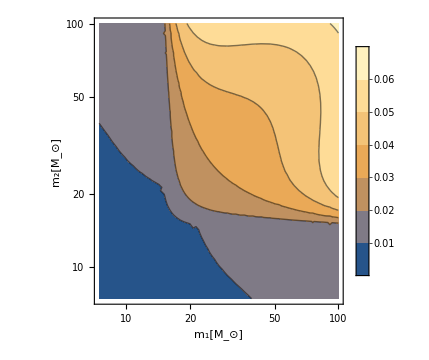

```mathematica
ContourPlot[ratioR[f0,i,j,α0,M0],{i,M0,mMax},{j,M0,mMax},FrameLabel->{"m_1[M_⊙]","m_2[M_⊙]"},ScalingFunctions->{"Log","Log"},FrameStyle->FontFamily->"Times",BaseStyle->FontSize->14,LabelStyle->GrayLevel[0],Frame->True,Axes->False,PlotRangePadding->None,ImageSize->360,AspectRatio->1,PlotLegends->Automatic]
(*Export["../latex/ratio-power.pdf",%]*)
```

```mathematica
Clear@R0;
R0[f_?NumericQ,α_?NumericQ,M_:M0]:=R0[f,α,M]=NIntegrate[mergerRateDensity[f,m1,m2,α,M],{m1,M,mMax},{m2,M,mMax},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
R0[f0,α0]//AbsoluteTiming
```

{0.071704,49.2469}

## Likelihood

## β2Inter - Interpolation of β2

```mathematica
βR0Inter=Interpolation@Import[".//backups//"<>model<>"_βR0Data"<>".m"]
Plot3D[βR0Inter[logf0,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

pdαSumInter - Interpolation of pdαSum

```mathematica
pdSumInter=Interpolation@Import[".//backups//"<>model<>"_pdSumData"<>".m"]
Plot3D[pdSumInter[logf0,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

## Posteriors

```mathematica
postNorm=NIntegrate[10^logf*10^logM*ⅇ^(-βR0Inter[logf,α,logM])*ⅇ^pdSumInter[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

3.04081×10^-17

```mathematica
post[logf_?NumericQ,α_?NumericQ,logM_?NumericQ]:=post[logf,α,logM]=1/postNorm*10^logf*10^logM*ⅇ^(-βR0Inter[logf,α,logM])*ⅇ^pdSumInter[logf,α,logM]

post[logf0,α0,logM0]//AbsoluteTiming

NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

{0.000122,0.0112318}

1.

## Contour plots

1D Marginalized posteriors

## Credible intervals

```mathematica
Clear[cdf,lower,upper,median];
```

```mathematica
cdf[para_?StringQ,y_?NumericQ]:=cdf[para,y]=NIntegrate[marginalPosterior1D[para,x],{x,min[para],y},PrecisionGoal->3];lower[para_?StringQ]:=lower[para]=x/.FindRoot[cdf[para,x]==0.05,{x,min[para],max[para]},PrecisionGoal->3];
upper[para_?StringQ]:=upper[para]=x/.FindRoot[cdf[para,x]==0.95,{x,min[para],max[para]},PrecisionGoal->3];
median[para_?StringQ]:=median[para]=x/.FindRoot[cdf[para,x]==0.5,{x,min[para],max[para]},PrecisionGoal->3];

minus[x_?StringQ]:=lower[x]-median[x];
plus[x_?StringQ]:=upper[x]-median[x];
range[x_?StringQ]:={lower[x],median[x],upper[x],plus[x],minus[x]}
```

## logf parameter

```mathematica
NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]
```

1.

```mathematica
marginalPosterior1D["logf",logf_?NumericQ]:=marginalPosterior1D["logf",logf]=NIntegrate[post[logf,α,logM],{α,min["α"],max["α"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

NIntegrate[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{10.8679,1.00027}

```mathematica
range["logf"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logf",range["logf"][[ii]]],{ii,3}]
```

{139.465,{-2.78192,-2.54874,-2.33827,0.233184,0.210461}}

{0.00165227,0.0028266,0.00458908,1.71074,1.62353}

{0.05,0.5,0.95}

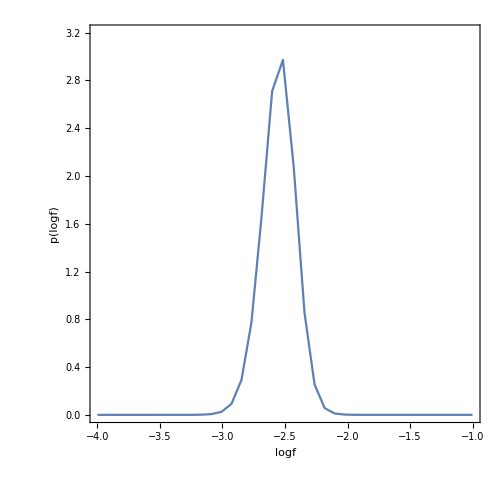

```mathematica
plot1D["logf"]=Plot[marginalPosterior1D["logf",logf],{logf,min["logf"],max["logf"]},PlotRange->{All,{0.0,3.2}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2,FrameLabel -> {"logf", "p(logf)"}]
```

## α parameter

```mathematica
marginalPosterior1D["α",α_?NumericQ]:=marginalPosterior1D["α",α]=NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},{logM,min["logM"],max["logM"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]

NIntegrate[marginalPosterior1D["α",α],{α,min["α"],max["α"]},PrecisionGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]//AbsoluteTiming
```

{11.5719,1.00026}

```mathematica
range["α"]//AbsoluteTiming
Table[cdf["α",range["α"][[ii]]],{ii,3}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{236.543,{1.53342,2.40811,3.40679,0.874687,0.998675}}

{0.05,0.500531,0.95}

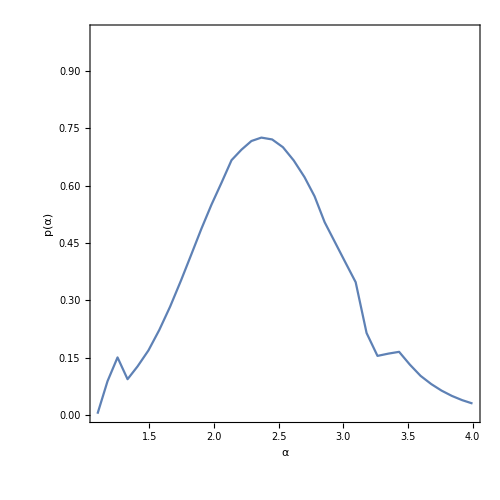

```mathematica
plot1D["α"]=Plot[marginalPosterior1D["α",α],{α,1.1,max["α"]},PlotRange->{All,{0,1.0}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->2,FrameLabel -> {"α", "p(α)"}]
```

## logM parameter

```mathematica
marginalPosterior1D["logM",logM_?NumericQ]:=marginalPosterior1D["logM",logM]=NIntegrate[post[logf,α,logM],{α,min["α"],max["α"]},{logf,min["logf"],max["logf"]},PrecisionGoal->3]

NIntegrate[marginalPosterior1D["logM",logM],{logM,min["logM"],max["logM"]},PrecisionGoal->3]
```

1.00044

```mathematica
range["logM"]//AbsoluteTiming
10^(%[[2]])
Table[cdf["logM",range["logM"][[ii]]],{ii,3}]
```

{149.579,{0.614249,0.871411,0.945433,0.257162,0.0740221}}

{4.11386,7.43722,8.81928,1.80785,1.18583}

{0.05,0.5,0.95}

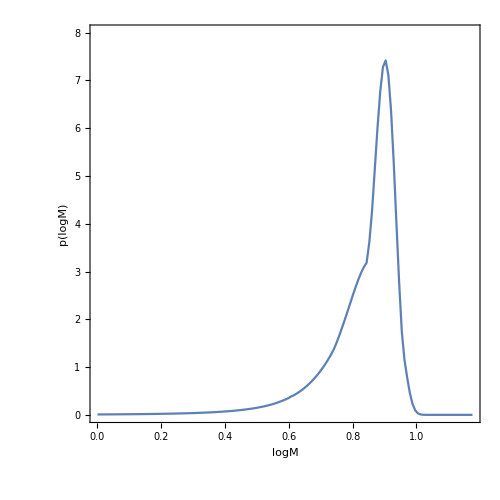

```mathematica
plot1D["logM"]=Plot[marginalPosterior1D["logM",logM],{logM,min["logM"],max["logM"]},PlotRange->{All,{0.0,8}},Evaluate@plotOptions,PlotPoints->10,MaxRecursion->4,FrameLabel -> {"logM", "p(logM)"}]
```

## R parameter

```mathematica
{10^median["logf"],median["α"],10^median["logM"]}
```

{0.0028266,2.40811,7.43722}

```mathematica
R0Fit=R0[10^median["logf"],median["α"],10^median["logM"]]
```

49.2469

```mathematica
βR0Inter[median["logf"],median["α"],median["logM"]]
```

6.81701

```mathematica
R0Post[R0_]:=R0^nBinary*ⅇ^(-R0 βR0Inter[median["logf"],median["α"],median["logM"]]/R0Fit)
```

```mathematica
normR=NIntegrate[R0Post[R],{R,min["R"],max["R"]}];
marginalPosterior1D["R",R_?NumericQ]:=R0Post[R]/normR;

NIntegrate[marginalPosterior1D["R",R],{R,min["R"],max["R"]}]
```

1.

```mathematica
range["R"]//AbsoluteTiming
```

{0.128057,{23.7335,48.1822,85.5508,24.4487,37.3686}}

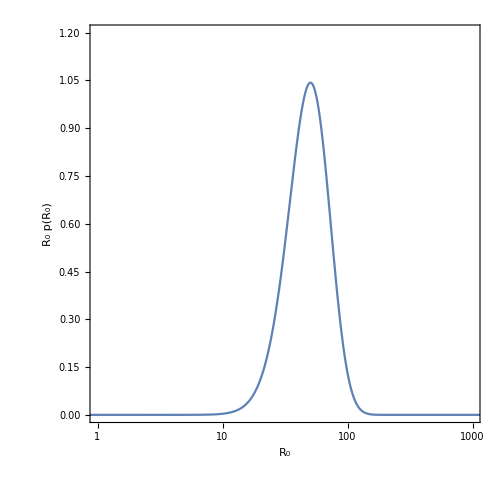

```mathematica
p2=LogLinearPlot[R*marginalPosterior1D["R",R],{R,min["R"],max["R"]},Evaluate@plotOptions,FrameLabel -> {"R_0", "R_0 p(R_0)"},PlotRange->{{1,10^3},{0,1.2}},FrameTicks->{{None,None},{True,None}}]
```

2D Marginalized posteriors

```mathematica
Clear[posteriorFit,marginalPosterior2D,marginalPosterior2DPlot];
posteriorFit[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2]=FindMaximum[marginalPosterior2D[para1,para2,x1,x2],{x1,median[para1],min[para1],max[para1]},{x2,median[para2],min[para2],max[para2]},PrecisionGoal->3]

constours[para1_?StringQ,para2_?StringQ]:=posteriorFit[para1,para2][[1]]*ⅇ^-dx2;
marginalPosterior2DPlot[para1_?StringQ,para2_?StringQ,opts:OptionsPattern[]]:=ContourPlot[marginalPosterior2D[para1,para2,x1,x2],{x1,min[para1]+0.05,max[para1]-0.1},{x2,min[para2]+0.05,max[para2]-0.1},Contours->constours[para1,para2],Evaluate[contourPlotOptions,plotOptions],opts]
```

## α-logM

{6.32554,{x1→2.58823,x2→0.899986}}

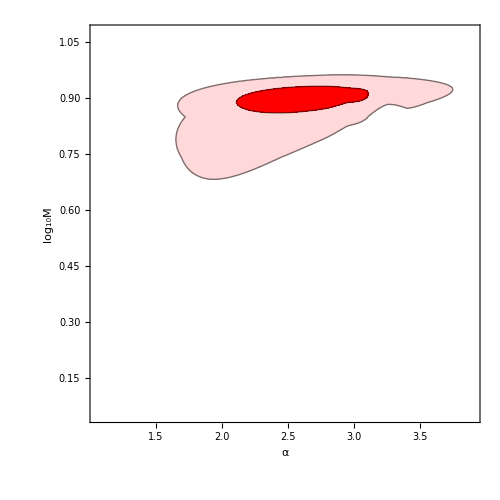

```mathematica
marginalPosterior2D["α","logM",α_?NumericQ,logM_?NumericQ]:=NIntegrate[post[logf,α,logM],{logf,min["logf"],max["logf"]},PrecisionGoal->3]

posteriorFit["α","logM"]

p1=plot2D["α","logM"]=marginalPosterior2DPlot["α","logM",PlotRange->{{1.5,4},{0.5,1}},PlotPoints->50,MaxRecursion->2,FrameLabel -> {"α","log_10M"},FrameTicks->{{True,None},{True,True}}]
```

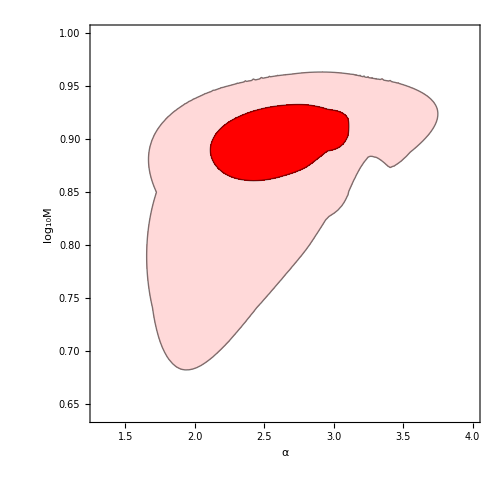

```mathematica
p3=Show[p1,PlotRange->{{1.3,4},{0.64,1}},FrameTicks->{{True,True},{True,True}}]
```

## Results

```mathematica
p1=-Graphics-;
p20=-Graphics-;
```

```mathematica
plotOptions0=Sequence[FrameStyle->(FontFamily->"Times"),BaseStyle->FontSize->25,LabelStyle->Black,Frame->True,Axes->False,PlotRangePadding->None,ImageSize->500,AspectRatio->1];
```

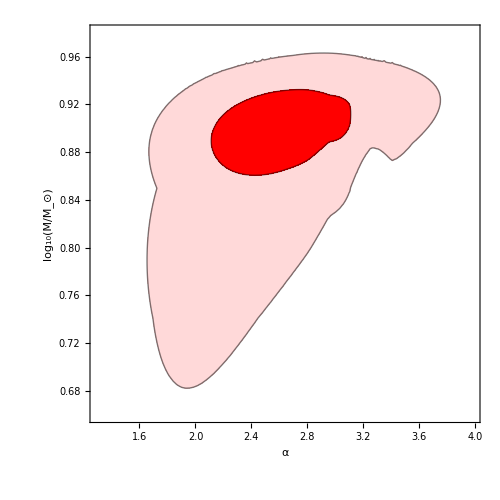

```mathematica
p3=Show[p1,PlotRange->{{1.3,3.98},{0.66,0.98}},FrameTicks->{{True,True},{True,True}},Evaluate@plotOptions0,FrameLabel -> {"α","log_10(M/M_⊙)"}]
```

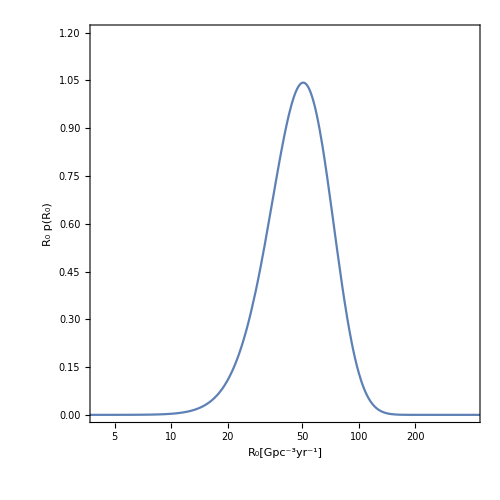

```mathematica
p2=Show[p20,Evaluate@plotOptions0,PlotRange->{{1.4,6},{0,1.2}},FrameLabel-> {"R_0[Gpc^-3yr^-1]", "R_0 p(R_0)"}]
```

```mathematica
range["logM"]
t1=10^range["logM"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{0.614249,0.871411,0.945433,-0.257162,0.0740221}

{4.11386,7.43722,8.81928,0.553144,1.18583}

{7.43722,1.38205,-3.32337}

```mathematica
range["logf"]
t1=10^range["logf"]
{t1[[2]],t1[[3]]-t1[[2]],t1[[1]]-t1[[2]]}
```

{-2.78192,-2.54874,-2.33827,0.210461,-0.233184}

{0.00165227,0.0028266,0.00458908,1.62353,0.584542}

{0.0028266,0.00176248,-0.00117433}

```mathematica
range["α"]
```

{1.53342,2.40811,3.40679,0.998675,-0.874687}

```mathematica
range["R"]
```

{23.7335,48.1822,85.5508,37.3686,-24.4487}

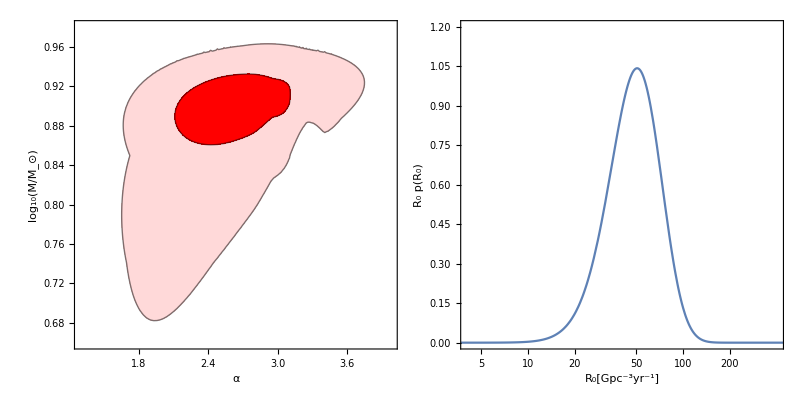

../latex/posterior-power.pdf

```mathematica
GraphicsGrid[{{p3,p2}},ImageSize->800,Spacings->Scaled[-.1]]
Export["../latex/posterior-power.pdf",%]
```